```mathematica
ClearAll["Global`*"]
```

```mathematica
t2[r_, t_, i_, s_]:=(i-1)/(2s)t+(s-1)/(2i)r+r/(2i*s)*t;
t1[r_, t_, i_, s_]:=-2 √(r*t*(2i-r)*(2s-t));
EAM[r_, t_, i_, s_]:=t1[r, t, i, s]+t2[r, t, i ,s];
```

### Contour Plots for EAM

```mathematica
tmax=10;
rmax =10;
```

```mathematica
cp[f_,rmax_, tmax_]:=ContourPlot[f[r, t],{r,0,rmax},{t,0,tmax},PlotLegends->Automatic , Contours->20, FrameStyle->Directive[Black, Thick], FrameLabel->{"r","t"},LabelStyle->{18, Black, FontFamily->"Helvetica"} ,ClippingStyle->Automatic];
```

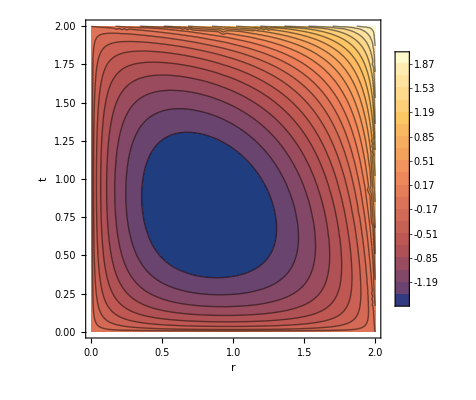

```mathematica
p0={1,1};
f0[r_,t_]:=EAM[r, t,p0[[1]],p0[[2]]];
cp[f0,2p0[[1]],2p0[[2]]]
```

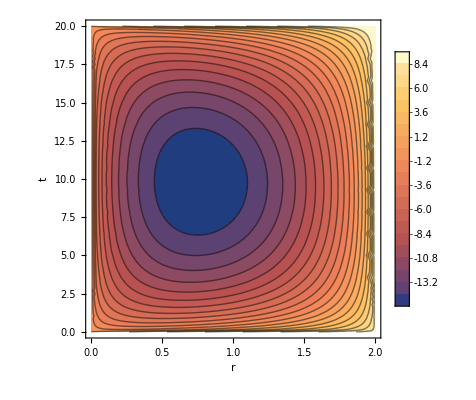

```mathematica
p1={1,10};
f1[r_,t_]:=EAM[r, t,p1[[1]],p1[[2]]];
cp[f1,2p1[[1]],2p1[[2]]]
```

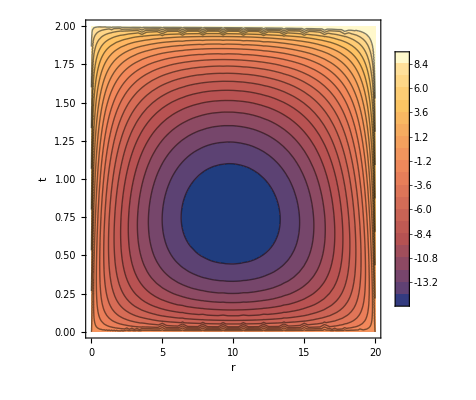

```mathematica
p2={10,1};
f2[r_,t_]:=EAM[r, t,p2[[1]],p2[[2]]];
cp[f2,2p2[[1]],2p2[[2]]]
```

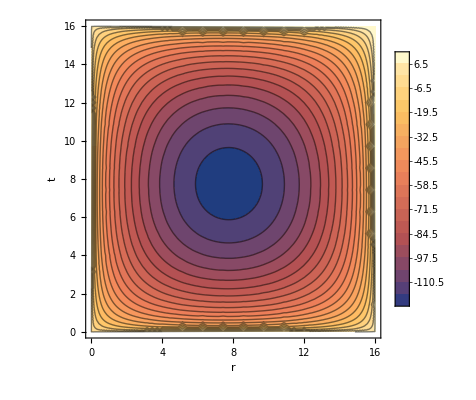

```mathematica
p3={8,8};
f3[r_,t_]:=EAM[r, t, p3[[1]],p3[[2]]];
cp[f3,2p3[[1]],2p3[[2]]]
```

### Minima points for EAM